# QFT compilation on Delft’s Silicon device

Connectivity of this device

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

Set the default configuration of the device

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_,list_]:=Module[{nansatz,simpncirc,fdist,ρ,qubits,ancillas,bells,ψ,uqubits,time,results,sdate},
sdate=Date[];
results=CircuitSynthesis[qubitsnum,conf];
time=DateDifference[sdate,Date[],"Minutes"];
{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}=results;
AppendTo[list,{conf,time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}];

nansatz=noisyAnsatz[ansatz/.θvars,conf][[1]];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
(* Fidelity distance *)
ρ=CreateDensityQureg[qubitsnum*2];
ψ=CreateQureg[qubitsnum*2];
uqubits=Range[0,-1+IntegerPart[Log2@Length@unitary]];
qubits=Range[0,qubitsnum-1];
ancillas=Range[qubitsnum,qubitsnum*2-1];
bells=Flatten[{Subscript[H, #[[1]]],Subscript[C, #[[1]]][Subscript[X, #[[2]]]]}&/@(Transpose[{qubits,ancillas}])];
ApplyCircuit[ρ,bells];
ApplyCircuit[ψ,bells];
ApplyCircuit[ρ,{Subscript[U, Sequence@@uqubits][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,simpncirc];

fdist=1-CalcFidelity[ρ,ψ];
DestroyQureg[ρ];
DestroyQureg[ψ];

Print["simulation time:",time," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[ansatz,qubitsnum];
Print["cost:",Elist[[-1]]];
Print["dist_fid=",fdist];
]
```

## The real device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->10^5,
(* T2^* : Implementation might be incorrect *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations: 5 is average *)
RabiFreq-><|0->5,1->5,2->5,3->5,4->5,5->5|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,

(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,

(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9239537120590723,1->0.9241761025557745,2->0.9166807085341168,3->0.9805456134451412,4->0.9649648861853775|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,1},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2
*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->0.99,
DurRead->10,
RepeatRead->2
};
```

## On the real setting: complete failure

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5,{3,4,5}];
```

Compilation with automatically generated ansatz at Tue 20 Sep 2022 15:33:10

@cycle1:Tue 20 Sep 2022 16:01:45, fev:457, <E>: 0.6409719629067536 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 18, 82}

@cycle2:Tue 20 Sep 2022 16:20:30, fev:640, <E>: 0.589621026186998 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 18, 136}

I'm slowing down @cycle 3

@cycle3:Tue 20 Sep 2022 16:29:44, fev:674, <E>: 0.589621026186998 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 18, 192}

I'm slowing down @cycle 4

@cycle4:Tue 20 Sep 2022 16:43:53, fev:707, <E>: 0.589621026186998 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 18, 326}

compile time:453.219 minutes; total iterations 972

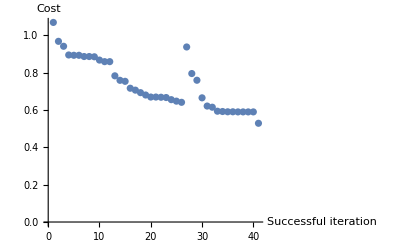

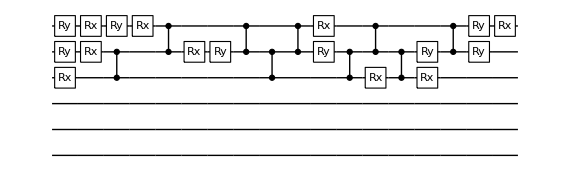

prob(0):<|3→0.334358,4→0.316218,5→0.349424|>

dist_fid=0.999871

Compilation with automatically generated ansatz at Tue 20 Sep 2022 17:10:01

@cycle1:Wed 21 Sep 2022 03:07:41, fev:633, <E>: 0.8445733708691557 nansatz: 1 merged-smallθ-metric-bf-gmerged: {6, 12, 0, 124, 372}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 03:57:34, fev:668, <E>: 0.8445733708691557 nansatz: 1 merged-smallθ-metric-bf-gmerged: {6, 12, 0, 124, 606}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 07:07:47, fev:706, <E>: 0.8445733708691557 nansatz: 1 merged-smallθ-metric-bf-gmerged: {6, 12, 0, 124, 1111}

compile time:1701.48 minutes; total iterations 728

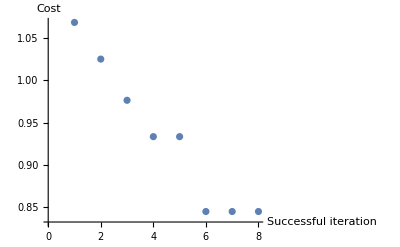

-Graphics-

prob(0):<|3→0.311505,4→0.379747,5→0.308748|>

dist_fid=0.999648

Compilation with automatically generated ansatz at Wed 21 Sep 2022 07:07:56

$Aborted

```mathematica
Table[
CompileCirc[conf,unitary,6,sidelft]
,{3}]
```

Using the parameter shift

Compilation with automatically generated ansatz at Wed 21 Sep 2022 12:16:33

@cycle1:Wed 21 Sep 2022 12:34:12, fev:229, <E>: 0.7579619550167681 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 113}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 12:39:39, fev:253, <E>: 0.7579619550167681 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 184}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 12:54:37, fev:283, <E>: 0.7579619550167681 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 342}

simulation time:43.1878 min minutes; total iterations 347

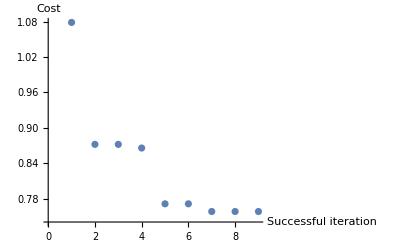

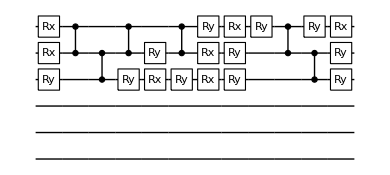

cost:0.757962

dist_fid=0.999975

Compilation with automatically generated ansatz at Wed 21 Sep 2022 12:59:51

@cycle1:Wed 21 Sep 2022 13:17:18, fev:357, <E>: 0.748443086184588 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 12, 129}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 13:23:15, fev:394, <E>: 0.748443086184588 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 12, 206}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 13:34:46, fev:421, <E>: 0.748443086184588 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 12, 346}

simulation time:35.9038 min minutes; total iterations 469

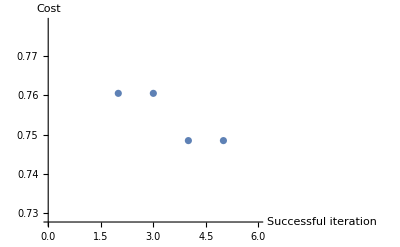

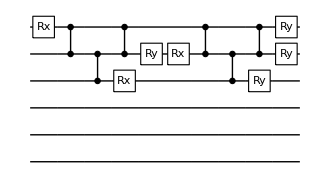

cost:0.6795

dist_fid=0.999095

{Null,Null}

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
DestroyAllQuregs[];

Table[
conf=checkedConf[dev,unitary,5,{3,4,5}];
conf["grad"]="GPS";
CompileCirc[conf,unitary,6,sidelft]
,{2}]
```

Compilation with automatically generated ansatz at Wed 21 Sep 2022 14:06:03

@cycle1:Wed 21 Sep 2022 14:25:58, fev:1245, <E>: 0.6166783179722367 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 20, 111}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 14:28:17, fev:1279, <E>: 0.6166783179722367 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 20, 160}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 14:34:06, fev:1307, <E>: 0.6166783179722367 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 20, 266}

simulation time:28.4377 min minutes; total iterations 1911

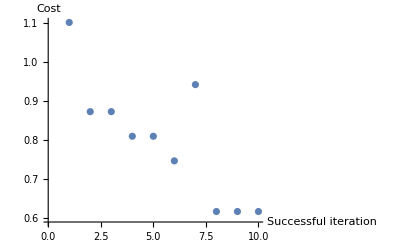

-Graphics-

cost:0.616678

dist_fid=0.981114

Compilation with automatically generated ansatz at Wed 21 Sep 2022 14:34:31

@cycle1:Wed 21 Sep 2022 15:40:25, fev:699, <E>: 0.7717635190786488 nansatz: 3 merged-smallθ-metric-bf-gmerged: {8, 1, 0, 23, 107}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 15:43:22, fev:728, <E>: 0.7717635190786488 nansatz: 3 merged-smallθ-metric-bf-gmerged: {8, 1, 0, 23, 182}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 15:51:13, fev:754, <E>: 0.7717635190786488 nansatz: 3 merged-smallθ-metric-bf-gmerged: {8, 1, 0, 23, 341}

simulation time:76.752 min minutes; total iterations 766

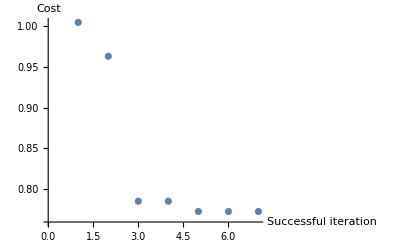

-Graphics-

cost:0.771764

dist_fid=0.999734

{Null,Null}

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
DestroyAllQuregs[];

Table[
conf=checkedConf[dev,unitary,5,{3,4,5}];
conf["grad"]="GPS";
CompileCirc[conf,unitary,6,sidelft]
,{2}]
```

```mathematica
unitary=N@CalcCircuitMatrix@QFT@6;
```

Compilation with automatically generated ansatz at Wed 21 Sep 2022 23:54:05

@cycle1:Thu 22 Sep 2022 01:11:42, fev:453, <E>: 0.870457016482704 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 72}

I'm slowing down @cycle 2

@cycle2:Thu 22 Sep 2022 01:29:34, fev:485, <E>: 0.870457016482704 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 148}

I'm slowing down @cycle 3

@cycle3:Thu 22 Sep 2022 02:07:02, fev:514, <E>: 0.870457016482704 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 294}

simulation time:141.225 min minutes; total iterations 564

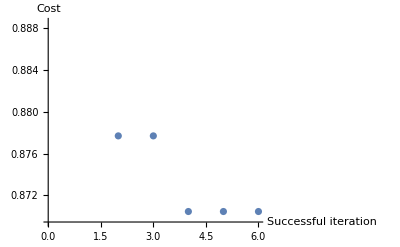

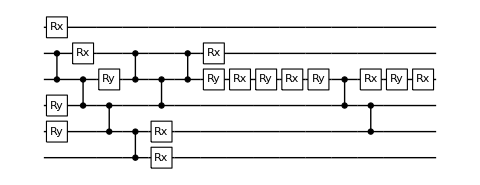

cost:0.870457

dist_fid=0.999795

Compilation with automatically generated ansatz at Thu 22 Sep 2022 02:15:27

@cycle1:Thu 22 Sep 2022 03:54:44, fev:428, <E>: 0.8148429101410927 nansatz: 9 merged-smallθ-metric-bf-gmerged: {6, 2, 0, 17, 89}

I'm slowing down @cycle 2

@cycle2:Thu 22 Sep 2022 04:03:52, fev:458, <E>: 0.8148429101410927 nansatz: 9 merged-smallθ-metric-bf-gmerged: {6, 2, 0, 17, 147}

I'm slowing down @cycle 3

@cycle3:Thu 22 Sep 2022 04:22:43, fev:480, <E>: 0.8148429101410927 nansatz: 9 merged-smallθ-metric-bf-gmerged: {6, 2, 0, 17, 258}

simulation time:129.282 min minutes; total iterations 543

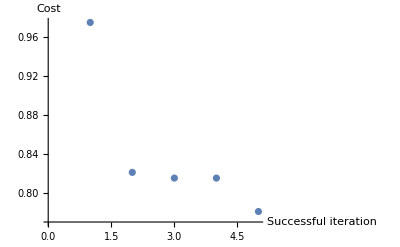

-Graphics-

cost:0.78049

dist_fid=0.999993

{Null,Null}

```mathematica
Table[
DestroyAllQuregs[];
dev=SiliconDelft[];
conf=checkedConf[dev,unitary,12,{0,1,2,3,4,5}];
conf["grad"]="GPS";
conf["ansatzspace"]={0,1,2,3,4,5};
CompileCirc[conf,unitary,6,sidelft]
,{2}]
```

```mathematica
sidelft//Length
```

9

## Early observation

{conf, time, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, probzeros, qmiavg, elimmerge, elimbfsmall, elimmetov, elimbf}

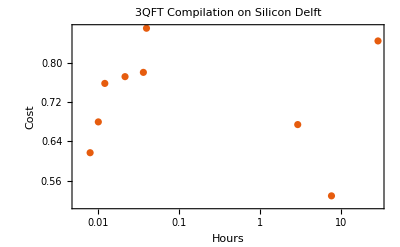

```mathematica
ListLogLinearPlot[Transpose@{sidelft[[All,2]]/3600,Last/@sidelft[[All,3]]},PlotTheme->"Scientific",FrameLabel->{"Hours","Cost"},PlotLabel->"3QFT Compilation on Silicon Delft",Background->White]
```

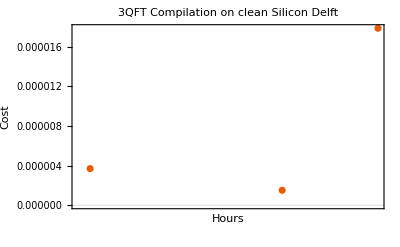

```mathematica
ListLogLinearPlot[Transpose@{sidelftclean[[All,2]]/3600,Last/@sidelftclean[[All,3]]},PlotTheme->"Scientific",FrameLabel->{"Hours","Cost"},PlotLabel->"3QFT Compilation on clean Silicon Delft",Background->White]
```

## Try using the zero extrapolation error mitigation

```mathematica
Options@SiliconDelft2=Options@SiliconDelft;
```

```mathematica
dev1=SiliconDelft[];
dev2=SiliconDelft2[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev1,unitary,5,{3,4,5}];
conf["device2"]=dev2;
sidelftmitig={};
```

```mathematica
CompileCirc[conf,unitary,6,sidelftmitig]
```

Compilation with automatically generated ansatz at Thu 22 Sep 2022 15:39:22

Part::partw: Part {2,3} of QuEST`Private`getSymbCtrlsTargs[{C_0[Z_1],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],Deph_0[0.],Depol_0[0.],Deph_1[0.],«695»}] does not exist.

Part::pkspec1: The expression 1+QuEST`Private`getSymbCtrlsTargs[{C_0[Z_1],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],Deph_0[0.],Depol_0[0.],Deph_1[0.],«695»}]⟦{2,3}⟧ cannot be used as a part specification.

Part::partw: Part {2,3} of QuEST`Private`getSymbCtrlsTargs[{C_0[Z_1],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],«906»}] does not exist.

Part::pkspec1: The expression 1+QuEST`Private`getSymbCtrlsTargs[{C_0[Z_1],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],«906»}]⟦{2,3}⟧ cannot be used as a part specification.

Part::partw: Part {2,3} of QuEST`Private`getSymbCtrlsTargs[{C_0[Z_1],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],«906»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression 1+QuEST`Private`getSymbCtrlsTargs[{C_0[Z_1],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],Depol_(0,1)[0.],Deph_(0,1)[0.0950579],C_1[Rz_2[0.023]],«906»}]⟦{2,3}⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted